# Supernova Database Statistics

### Setup/Imports

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

```mathematica
linTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,1}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,Which[!IntegerQ[i/interval],MaTeX["",Magnification->magnification],i==0,MaTeX[1,Magnification->magnification],i==1,MaTeX[10,Magnification->magnification],True,MaTeX[Power[10,ToString[i]],Magnification->magnification]],{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])

linTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])
```

```mathematica
color[i_]:=ColorData[97,"ColorList"][[i]];
changeStyle[col_][Graphics[items_,opt___]]:=Graphics[{col,items},opt]
```

```mathematica
(*Find roots more accurately than Mathematica's FindRoot. Used later to find axion decay temperature*)
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}];
```

### Data

```mathematica
(*data2023=Import["https://www.physics.purdue.edu/brightsupernovae/sn2023/sndate.html","Data"]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"SNdata2023.m",data2023]*)
```

```mathematica
data2023=Import[NotebookDirectory[]<>"Data/SNdata2023.m"]
```

```mathematica
magPos=FirstPosition[data2023[[2,1]],"Mag"][[1]]
maxMagPos=FirstPosition[data2023[[2,1]],"Mag Max"][[1]]
```

9

10

```mathematica
data2023[[2,2,9]]
```

18.1

```mathematica
magTabSN2023Raw=Table[data2023[[2,i,magPos]],{i,2,Length[data2023[[2]]]}]
```

```mathematica
magTabSN2023=Table[
element=magTabSN2023Raw[[i]];
cleanedElement=Which[StringQ[element],StringDelete[element,"*"...],True,element];
ToExpression[cleanedElement],{i,1,Length[magTabSN2023Raw]}]
```

```mathematica
snHistogram2023=Histogram[magTabSN2023,{.1},Frame->True,FrameTicks->{{linTick[0,800,1.5,100],linTickNone[0,800,1.5,100]},{linTick[10,25,1.5,2],linTickNone[10,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],{14,550}]}]
```

-Graphics-

```mathematica
snHistogram2023Zoom=Histogram[magTabSN2023,{.1},
PlotRange->{{10,15},{0,10}},
PlotRangePadding->None,
Frame->True,
FrameTicks->{{linTick[0,10,1.5,1],linTickNone[0,10,1.5,1]},{linTick[10,25,1.5,1],linTickNone[10,25,1.5,1]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],{14,550}]}]
```

-Graphics-

```mathematica
snHistogram2023Total=Grid[{{snHistogram2023,snHistogram2023Zoom}}]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"snHistogram2023Total.pdf",snHistogram2023Total]*)
```

```mathematica
Min[magTabSN2023]
Max[magTabSN2023]
Mean[magTabSN2023]
Median[magTabSN2023]
```

10.4

29.5

19.9268

20.

```mathematica
peakMagTabSN2023Raw=Table[data2023[[2,i,maxMagPos]],{i,2,Length[data2023[[2]]]}]
```

```mathematica
peakMagTabSN2023=Table[
element=peakMagTabSN2023Raw[[i]];
cleanedElement=Which[StringQ[element],StringDelete[element,"*"...],True,element];
ToExpression[cleanedElement],{i,1,Length[peakMagTabSN2023Raw]}]
```

```mathematica
peaksnHistogram2023=Histogram[peakMagTabSN2023,{.1},Frame->True,FrameTicks->{{linTick[0,800,1.5,100],linTickNone[0,800,1.5,100]},{linTick[10,25,1.5,2],linTickNone[10,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Peak Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],{14,550}]}]
```

-Graphics-

### Type

```mathematica
typePos=FirstPosition[data2023[[2,1]],"Type"][[1]]
```

8

```mathematica
typeTabSN2023Raw=Table[data2023[[2,i,typePos]],{i,2,Length[data2023[[2]]]}];
```

```mathematica
typeTabSN2023Numbered=Table[
element=typeTabSN2023Raw[[i]];
{i,Switch[element,"Ia",1,"II",2,"IIP",3,"Ic",4,"Ic-BL",4,"unk",5,_,6]},{i,1,Length[typeTabSN2023Raw]}];
```

```mathematica
snSubtypeHistogram=Histogram[Transpose[typeTabSN2023Numbered][[2]],Automatic,"LogCount",Frame->True,FrameTicks->{Automatic,{{{1,"Ia"},{2,"II"},{3,"IIp"},{4,"Ic"},{5,"Unknown"},{6,"Other"}},None}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{SN Type}",Magnification->1.5],None}},ImageSize->500,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]]}]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"snSubtypeHistogram.pdf",snSubtypeHistogram]*)
```

```mathematica
indicesTab=GatherBy[typeTabSN2023Numbered,Last]
```

```mathematica
indicesTypeI=Transpose[indicesTab[[1]]][[1]];
indicesTypeII=Transpose[indicesTab[[3]]][[1]];
indicesTypeIIp=Transpose[indicesTab[[6]]][[1]];
indicesTypeIc=Transpose[indicesTab[[5]]][[1]];
indicesTypeUnknown=Transpose[indicesTab[[2]]][[1]];
indicesTypeOther=Transpose[indicesTab[[4]]][[1]];
```

```mathematica
magTabSN2023TypeI=Table[magTabSN2023[[i]],{i,indicesTypeI}];
magTabSN2023TypeII=Table[magTabSN2023[[i]],{i,indicesTypeII}];
magTabSN2023TypeIIp=Table[magTabSN2023[[i]],{i,indicesTypeIIp}];
magTabSN2023TypeIc=Table[magTabSN2023[[i]],{i,indicesTypeIc}];
magTabSN2023TypeUnknown=Table[magTabSN2023[[i]],{i,indicesTypeUnknown}];
magTabSN2023TypeOther=Table[magTabSN2023[[i]],{i,indicesTypeOther}];
```

```mathematica
snHistogram2023TypeI=Histogram[magTabSN2023TypeI,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type I}",Magnification->2.0],0Degree]],Scaled[{.125,.7}]]}]
```

-Graphics-

```mathematica
snHistogram2023TypeII=Histogram[magTabSN2023TypeII,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type II}",Magnification->2.0],0Degree]],Scaled[{.125,.7}]]}]
```

-Graphics-

```mathematica
snHistogram2023TypeIIp=Histogram[magTabSN2023TypeIIp,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type IIp}",Magnification->2.0],0Degree]],Scaled[{.125,.7}]]}]
```

-Graphics-

```mathematica
snHistogram2023TypeIc=Histogram[magTabSN2023TypeIc,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type Ic}",Magnification->2.0],0Degree]],Scaled[{.125,.7}]]}]
```

-Graphics-

```mathematica
snHistogram2023TypeOther=Histogram[magTabSN2023TypeOther,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type Other}",Magnification->2.0],0Degree]],Scaled[{.2,.7}]]}]
```

-Graphics-

```mathematica
snHistogram2023TypeUnknown=Histogram[magTabSN2023TypeUnknown,{.1},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Type Unknown}",Magnification->2.0],0Degree]],Scaled[{.25,.7}]]}]
```

-Graphics-

```mathematica
totalHistogramTypeCount=Histogram[{magTabSN2023TypeUnknown,magTabSN2023TypeOther,magTabSN2023TypeI,magTabSN2023TypeII,magTabSN2023TypeIc,magTabSN2023TypeIIp},Automatic,"LogCount",ChartLegends->{"Unknown","Other","Type I","Type II","Type Ic","Type IIp"},Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["\\text{Total}",Magnification->2.0],0Degree]],Scaled[{.12,.7}]]}]
```

-Graphics-

### Survey

```mathematica
surveyPos=FirstPosition[data2023[[2,1]],"Alternate names"][[1]]
```

12

```mathematica
surveyTabSN2023Raw=Table[data2023[[2,i,surveyPos]],{i,2,Length[data2023[[2]]]}]//Quiet;
```

```mathematica
Length[surveyTabSN2023Raw]
```

18436

```mathematica
(*
PanStarrs (PS23) = 1;
Zwicky or Alerce (ZTF) = 2;
ATLAS (ATLAS) = 3;
GAIA = 4;
*)

surveyTabSN2023Numbered=Table[
element=surveyTabSN2023Raw[[i]];
{i,Which[
StringContainsQ[element,"PS23"],1,
StringContainsQ[element,"ZTF"],2,
StringContainsQ[element,"ATLAS"],3,
(*StringContainsQ[element,"GAIA"],4,*)
True,4]},{i,1,Length[surveyTabSN2023Raw]}];//Quiet
```

```mathematica
Histogram[Transpose[surveyTabSN2023Numbered][[2]],Automatic,"LogCount",Frame->True,FrameTicks->{Automatic,{{{1,"PanStarr"},{2,"ZTF"},{3,"ATLAS"},(*{4,"GAIA"},*){4,"Other"}},None}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts}" ,Magnification->1.5],None},{MaTeX["\\text{SN Survey}",Magnification->1.5],None}},ImageSize->500,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.85}]]}]//Quiet
```

-Graphics-

```mathematica
panStarrIndices=Cases[surveyTabSN2023Numbered,{_,1}];
```

```mathematica
ztfIndices=Cases[surveyTabSN2023Numbered,{_,2}];
```

```mathematica
atlasIndices=Cases[surveyTabSN2023Numbered,{_,3}];
```

```mathematica
otherIndices=Cases[surveyTabSN2023Numbered,{_,4}];
```

```mathematica
panStarrMags=Table[peakMagTabSN2023[[panStarrIndices[[i,1]]]],{i,1,Length[panStarrIndices]}];
ztfMags=Table[peakMagTabSN2023[[ztfIndices[[i,1]]]],{i,1,Length[ztfIndices]}];
atlasMags=Table[peakMagTabSN2023[[atlasIndices[[i,1]]]],{i,1,Length[atlasIndices]}];
otherMags=Table[peakMagTabSN2023[[otherIndices[[i,1]]]],{i,1,Length[otherIndices]}];
```

```mathematica
snHistogramSurveys=Histogram[{panStarrMags,ztfMags,atlasMags,otherMags},{15,23,.1},Frame->True,
PlotRange->{{15,23},{0,500}},
PlotRangePadding->None,
FrameTicks->{{linTick[0,800,1.5,100],linTickNone[0,800,1.5,100]},{linTick[10,25,1.5,2],linTickNone[10,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Survey}" ,Magnification->1.5],None},{MaTeX["\\text{Peak Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.9}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],.1]]@MaTeX["\\text{PanStarrs}",Magnification->1.5],0Degree]],Scaled[{.425+.05,.875}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["\\text{ZTF}",Magnification->1.5],0Degree]],Scaled[{.8+.05,.75}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.1]]@MaTeX["\\text{ATLAS}",Magnification->1.5],0Degree]],Scaled[{.3+.05,.45}]],
Inset[Style[Rotate[changeStyle[Darker[color[4],.1]]@MaTeX["\\text{Other}",Magnification->1.5],0Degree]],Scaled[{.925,.05}]]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/SN_Histrogram_Surveys.pdf",snHistogramSurveys]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/SN_Histrogram_Surveys.pdf

```mathematica
snHistogramSurveysZoom=Histogram[{panStarrMags,ztfMags,atlasMags,otherMags},{10,15,.1},Frame->True,
PlotRange->{{10,15},{0,5}},
PlotRangePadding->None,
FrameTicks->{{linTick[0,10,1.5,1],linTickNone[0,800,1.5,100]},{linTick[10,25,1.5,1],linTickNone[10,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Survey}" ,Magnification->1.5],None},{MaTeX["\\text{Peak Magnitude}",Magnification->1.5],None}},ImageSize->500,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2023",Magnification->2.5],0Degree]],Scaled[{.1,.9}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],.1]]@MaTeX["\\text{PanStarrs}",Magnification->1.5],0Degree]],Scaled[{.3,.75}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.1]]@MaTeX["\\text{ZTF}",Magnification->1.5],0Degree]],Scaled[{.34,.65}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.1]]@MaTeX["\\text{ATLAS}",Magnification->1.5],0Degree]],Scaled[{.31,.55}]],
Inset[Style[Rotate[changeStyle[Darker[color[4],.1]]@MaTeX["\\text{Other}",Magnification->1.5],0Degree]],Scaled[{.32,.45}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["m \\leq 14",Magnification->1.75],0Degree]],Scaled[{.55,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["m \\leq 15",Magnification->1.75],0Degree]],Scaled[{.8,.85}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["10",Magnification->1.5],0Degree]],Scaled[{.55,.75}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["14",Magnification->1.5],0Degree]],Scaled[{.55,.65}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["10",Magnification->1.5],0Degree]],Scaled[{.55,.55}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["4",Magnification->1.5],0Degree]],Scaled[{.55,.45}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["4",Magnification->1.5],0Degree]],Scaled[{.8,.75}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["7",Magnification->1.5],0Degree]],Scaled[{.8,.65}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["1",Magnification->1.5],0Degree]],Scaled[{.8,.55}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX["1",Magnification->1.5],0Degree]],Scaled[{.8,.45}]]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"SN_Histrogram_Surveys_Zoom.pdf",snHistogramSurveysZoom]
```

/Users/david/Documents/Projects/EPIC Hubble/Mathematica/SN_Histrogram_Surveys_Zoom.pdf

```mathematica
maxMag=14;
snCountsLess15PanStarrs=Count[panStarrMags,mag_/;mag<=maxMag]
snCountsLess15ZTF=Count[ztfMags,mag_/;mag<=maxMag]
snCountsLess15Atlas=Count[atlasMags,mag_/;mag<=maxMag]
snCountsLess15Other=Count[otherMags,mag_/;mag<=maxMag]

(*snPeakCountsLess15=Table[{datesTab[[i]],Count[peakMagTabSNData[[i]],mag_/;mag<=maxMag]},{i,1,Length[datesTab]}]

maxMag2=14;
snCountsLess14=Table[{datesTab[[i]],Count[magTabSNData[[i]],mag_/;mag<=maxMag2]},{i,1,Length[datesTab]}]

snPeakCountsLess14=Table[{datesTab[[i]],Count[peakMagTabSNData[[i]],mag_/;mag<=maxMag2]},{i,1,Length[datesTab]}]*)
```

4

7

1

1

### Grid of Histograms

```mathematica
gridOfSNSubtypeStats=Grid[{{snHistogram2023TypeI,snHistogram2023TypeII},{snHistogram2023TypeIIp,snHistogram2023TypeIc},{snHistogram2023TypeOther,snHistogram2023TypeUnknown},{totalHistogramTypeCount}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export[NotebookDirectory[]<>"Figures/gridOfSNSubtypeStats.pdf",gridOfSNSubtypeStats]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/gridOfSNSubtypeStats.pdf

### Automation: Extraction of SN Population Data

##### Sorting

```mathematica
datesTab=Table[i,{i,2000,2024}];
```

```mathematica
(*snDataByMagTable=Table[Import["https://www.physics.purdue.edu/brightsupernovae/sn"<>ToString[dates]<>"/snmag.html","Data"],{dates,datesTab}];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"snDataByMag.m",snDataByMagTable]*)
```

```mathematica
snDataByMagTable=Import[NotebookDirectory[]<>"Data/snDataByMag.m"];
```

```mathematica
magPos2=7;
maxMagPos2=5;
typePos2=9;
```

```mathematica
magTabSNDataTableRaw2=Table[snDataByMagTable[[j,2,i,magPos2]],{j,1,Length[snDataByMagTable]},{i,2,Length[snDataByMagTable[[j,2]]]}];

peakMagTabSNDataTableRaw2=Table[snDataByMagTable[[j,2,i,maxMagPos2]],{j,1,Length[snDataByMagTable]},{i,2,Length[snDataByMagTable[[j,2]]]}];
```

```mathematica
snTypeTableRaw2=Table[snDataByMagTable[[j,2,i,typePos2]],{j,1,Length[snDataByMagTable]},{i,2,Length[snDataByMagTable[[j,2]]]}];
```

```mathematica
gatheredTypes=Gather[Flatten[snTypeTableRaw2]];
```

```mathematica
gatheredTypes2024=Gather[snTypeTableRaw2[[-1]]];
```

```mathematica
gatheredTypesRanking=Table[{gatheredTypes[[i,1]],Length[gatheredTypes[[i]]]},{i,1,Length[gatheredTypes]}]
```

{{EGV,264},{Ia-pec,173},{Ia,15256},{II,3678},{IIn,754},{Ic,632},{Radio,3},{Ibn,76},{unk,133638},{Ib,425},{IIb,376},{IIL,19},{LBV,63},{II-pec,36},{Ia-91bg,180},{Ia?,86},{II?,37},{Ib/c,172},{IIP,616},{X-Ray,4},{I,80},{IIn/LBV,11},{Ib/c-pec,3},{Ic-pec,15},{II,,1},{I?,1},{Ic?,7},{IIn-pec,12},{-,1},{II/Ib,1},{Ia:,1},{LRN,21},{IIb/Ib,1},{Ib-pec,19},{I-pec,3},{FeIIb,11},{FeII,161},{He/N,28},{He/Nn,1},{Mira,2},{Ia/Ic,2},{Ib?,2},{Ia/Ic?,1},{Ia/c?,1},{He,1},{IIn-pec/LBV,1},{Ibc,13},{II/LBV,1},{II-pec?,3},{Ib/IIb,4},{Ic-BL,157},{Ic/Ia,2},{I-faint,1},{hybrid,1},{Variable,1},{IIn/Ic,1},{M2,1},{SLSN-IIn,2},{SLSN,8},{IIn/Ibn,1},{IIn?,4},{USco,1},{Fe,1},{WR,1},{LBV?,7},{SLSN-Ic,4},{N/He,1},{Ia-91T,530},{Ic-pec?,2},{Ia-HV,3},{SLSN-I,177},{Ia-02cx,48},{Ia-csm,2},{Ia-CSM,36},{IIb?,1},{SLSN-II,95},{CCSN,3},{Ib/c?,3},{Iax,3},{SLSN-I?,3},{II-09ip,1},{EGN,56},{SN,94},{Kilonova,1},{Ia-CSM/IIn,1},{Ibn?,1},{Ibc?,1},{SLSN-II?,1},{Ia-SC,13},{SN?,1},{Ib/Ic,1},{ILRT,2},{Ia-99aa,3},{Ia/b,1},{Ib-Ca-rich,8},{Iz,5},{SNSN-II,1},{Icn,7},{LBV/IIn,1},{Ia-91T-like,1},{II/IIb,1},{WZ,1},{Iazhost=0.088376),1},{Ia-11kx,1},{Ib-18cow,1},{Ibn/Icn,3},{IIp,1},{Ia-00cx,1},{Ien,1},{FBOT,4},{SN!,1},{II/FBOT,1},{FBOT?,3},{Gap,1},{Ia-91bg-like,1}}

```mathematica
SortBy[gatheredTypesRanking,Last]
```

{{-,1},{Fe,1},{Gap,1},{He,1},{He/Nn,1},{hybrid,1},{I?,1},{Ia:,1},{Ia-00cx,1},{Ia-11kx,1},{Ia-91bg-like,1},{Ia-91T-like,1},{Ia/b,1},{Ia/c?,1},{Ia-CSM/IIn,1},{Ia/Ic?,1},{Iazhost=0.088376),1},{Ib-18cow,1},{Ibc?,1},{Ib/Ic,1},{Ibn?,1},{Ien,1},{I-faint,1},{II,,1},{II-09ip,1},{IIb?,1},{IIb/Ib,1},{II/FBOT,1},{II/Ib,1},{II/IIb,1},{II/LBV,1},{IIn/Ibn,1},{IIn/Ic,1},{IIn-pec/LBV,1},{IIp,1},{Kilonova,1},{LBV/IIn,1},{M2,1},{N/He,1},{SLSN-II?,1},{SN!,1},{SN?,1},{SNSN-II,1},{USco,1},{Variable,1},{WR,1},{WZ,1},{Ia-csm,2},{Ia/Ic,2},{Ib?,2},{Ic/Ia,2},{Ic-pec?,2},{ILRT,2},{Mira,2},{SLSN-IIn,2},{CCSN,3},{FBOT?,3},{Ia-99aa,3},{Ia-HV,3},{Iax,3},{Ib/c?,3},{Ib/c-pec,3},{Ibn/Icn,3},{II-pec?,3},{I-pec,3},{Radio,3},{SLSN-I?,3},{FBOT,4},{Ib/IIb,4},{IIn?,4},{SLSN-Ic,4},{X-Ray,4},{Iz,5},{Ic?,7},{Icn,7},{LBV?,7},{Ib-Ca-rich,8},{SLSN,8},{FeIIb,11},{IIn/LBV,11},{IIn-pec,12},{Ia-SC,13},{Ibc,13},{Ic-pec,15},{Ib-pec,19},{IIL,19},{LRN,21},{He/N,28},{Ia-CSM,36},{II-pec,36},{II?,37},{Ia-02cx,48},{EGN,56},{LBV,63},{Ibn,76},{I,80},{Ia?,86},{SN,94},{SLSN-II,95},{Ic-BL,157},{FeII,161},{Ib/c,172},{Ia-pec,173},{SLSN-I,177},{Ia-91bg,180},{EGV,264},{IIb,376},{Ib,425},{Ia-91T,530},{IIP,616},{Ic,632},{IIn,754},{II,3678},{Ia,15256},{unk,133638}}

```mathematica
excludedTypes={{"-",1},{"Fe",1},{"Gap",1},{"He",1},{"He/Nn",1},{"hybrid",1},{"Kilonova",1},{"LBV/IIn",1},{"M2",1},{"N/He",1},{"SLSN-II?",1},{"USco",1},{"Variable",1},{"WR",1},{"WZ",1},{"ILRT",2},{"Mira",2},{"SLSN-IIn",2},{"FBOT?",3},{"Radio",3},{"SLSN-I?",3},{"FBOT",4},{"SLSN-Ic",4},{"X-Ray",4},{"LBV?",7},{"SLSN",8},{"FeIIb",11},{"LRN",21},{"He/N",28},{"EGN",56},{"LBV",63},{"SLSN-II",95},{"FeII",161},{"SLSN-I",177},{"EGV",264}}
```

{{-,1},{Fe,1},{Gap,1},{He,1},{He/Nn,1},{hybrid,1},{Kilonova,1},{LBV/IIn,1},{M2,1},{N/He,1},{SLSN-II?,1},{USco,1},{Variable,1},{WR,1},{WZ,1},{ILRT,2},{Mira,2},{SLSN-IIn,2},{FBOT?,3},{Radio,3},{SLSN-I?,3},{FBOT,4},{SLSN-Ic,4},{X-Ray,4},{LBV?,7},{SLSN,8},{FeIIb,11},{LRN,21},{He/N,28},{EGN,56},{LBV,63},{SLSN-II,95},{FeII,161},{SLSN-I,177},{EGV,264}}

```mathematica
includedTypes=SortBy[Complement[gatheredTypesRanking,excludedTypes],Last]
```

{{I?,1},{Ia:,1},{Ia-00cx,1},{Ia-11kx,1},{Ia-91bg-like,1},{Ia-91T-like,1},{Ia/b,1},{Ia/c?,1},{Ia-CSM/IIn,1},{Ia/Ic?,1},{Iazhost=0.088376),1},{Ib-18cow,1},{Ibc?,1},{Ib/Ic,1},{Ibn?,1},{Ien,1},{I-faint,1},{II,,1},{II-09ip,1},{IIb?,1},{IIb/Ib,1},{II/FBOT,1},{II/Ib,1},{II/IIb,1},{II/LBV,1},{IIn/Ibn,1},{IIn/Ic,1},{IIn-pec/LBV,1},{IIp,1},{SN!,1},{SN?,1},{SNSN-II,1},{Ia-csm,2},{Ia/Ic,2},{Ib?,2},{Ic/Ia,2},{Ic-pec?,2},{CCSN,3},{Ia-99aa,3},{Ia-HV,3},{Iax,3},{Ib/c?,3},{Ib/c-pec,3},{Ibn/Icn,3},{II-pec?,3},{I-pec,3},{Ib/IIb,4},{IIn?,4},{Iz,5},{Ic?,7},{Icn,7},{Ib-Ca-rich,8},{IIn/LBV,11},{IIn-pec,12},{Ia-SC,13},{Ibc,13},{Ic-pec,15},{Ib-pec,19},{IIL,19},{Ia-CSM,36},{II-pec,36},{II?,37},{Ia-02cx,48},{Ibn,76},{I,80},{Ia?,86},{SN,94},{Ic-BL,157},{Ib/c,172},{Ia-pec,173},{Ia-91bg,180},{IIb,376},{Ib,425},{Ia-91T,530},{IIP,616},{Ic,632},{IIn,754},{II,3678},{Ia,15256},{unk,133638}}

```mathematica
excludedTypesWithoutCounts=Table[excludedTypes[[i,1]],{i,1,Length[excludedTypes]}]
```

{-,Fe,Gap,He,He/Nn,hybrid,Kilonova,LBV/IIn,M2,N/He,SLSN-II?,USco,Variable,WR,WZ,ILRT,Mira,SLSN-IIn,FBOT?,Radio,SLSN-I?,FBOT,SLSN-Ic,X-Ray,LBV?,SLSN,FeIIb,LRN,He/N,EGN,LBV,SLSN-II,FeII,SLSN-I,EGV}

```mathematica
gatheredTypes2024Ranking=Table[{gatheredTypes2024[[i,1]],Length[gatheredTypes2024[[i]]]},{i,1,Length[gatheredTypes2024]}]
```

{{II,350},{Ia,1426},{unk,19849},{Ia-pec,17},{Ic,47},{Ia-SC,4},{IIb,40},{Ib,24},{Ia-91T,48},{Ic-BL,20},{Ia-02cx,5},{IIn,50},{SN,23},{Ia-91bg,24},{FeII,3},{Icn,1},{EGN,5},{IIP,25},{SLSN-I,30},{Ib/c,7},{FBOT,2},{Ibn,7},{Ib-pec,3},{Ia-CSM,7},{SLSN-II,8},{EGV,1},{Gap,1},{Ib-Ca-rich,2},{II-pec,2},{Iz,1},{Ic?,2},{LBV,2},{Ia-91bg-like,1},{I,1}}

```mathematica
SortBy[gatheredTypes2024Ranking,Last]
```

{{EGV,1},{Gap,1},{I,1},{Ia-91bg-like,1},{Icn,1},{Iz,1},{FBOT,2},{Ib-Ca-rich,2},{Ic?,2},{II-pec,2},{LBV,2},{FeII,3},{Ib-pec,3},{Ia-SC,4},{EGN,5},{Ia-02cx,5},{Ia-CSM,7},{Ib/c,7},{Ibn,7},{SLSN-II,8},{Ia-pec,17},{Ic-BL,20},{SN,23},{Ia-91bg,24},{Ib,24},{IIP,25},{SLSN-I,30},{IIb,40},{Ic,47},{Ia-91T,48},{IIn,50},{II,350},{Ia,1426},{unk,19849}}

```mathematica
Table[
Which[MemberQ[excludedTypesWithoutCounts,snTypeTableRaw2[[1,i]]],0,True,1],{i,1,Length[snTypeTableRaw2[[1]]]}]
```

{0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

##### Cleaning Data

```mathematica
minMagnitude=9;
```

```mathematica
peakMagTabSNData2RemoveExtraneous=Table[
element=peakMagTabSNDataTableRaw2[[j,i]];
elementType=snTypeTableRaw2[[j,i]];
cleanedElement=Which[
element<minMagnitude,##&[],
MemberQ[excludedTypesWithoutCounts,elementType],##&[],
True,element];
cleanedElement,{j,1,Length[peakMagTabSNDataTableRaw2]},{i,1,Length[peakMagTabSNDataTableRaw2[[j]]]}];
```

```mathematica
magTabSNData2=Table[
element=magTabSNDataTableRaw2[[j,i]];
cleanedElement=Which[StringQ[element],StringDelete[element,"*"...],True,element];
ToExpression[cleanedElement],{j,1,Length[magTabSNDataTableRaw2]},{i,1,Length[magTabSNDataTableRaw2[[j]]]}];

peakMagTabSNData2=Table[
element=peakMagTabSNData2RemoveExtraneous[[j,i]];
cleanedElement=Which[StringQ[element],StringDelete[element,"*"...],True,element];
ToExpression[cleanedElement],{j,1,Length[peakMagTabSNData2RemoveExtraneous]},{i,1,Length[peakMagTabSNData2RemoveExtraneous[[j]]]}];
```

##### Analysis

```mathematica
snDataOverviewHistogram2=Histogram[magTabSNData2,{.1},Frame->True,
PlotRange->{{6,24},{0,950}},
FrameTicks->{{linTick[0,1000,1.5,100],linTickNone[0,1000,1.5,100]},{linTick[6,25,1.5,2],linTickNone[6,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Year}" ,Magnification->1.5],None},{MaTeX["\\text{Last Observation Magnitude}",Magnification->1.5],None}},ImageSize->500,PlotRangeClipping->True,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2000-2024",Magnification->2.5],0Degree]],{10,800}]}]

snDataOverviewHistogramPeakMag2=Histogram[peakMagTabSNData2,{.1},
PlotRange->{{6,24},{0,950}},Frame->True,FrameTicks->{{linTick[0,1000,1.5,100],linTickNone[0,1000,1.5,100]},{linTick[6,25,1.5,2],linTickNone[6,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Year}" ,Magnification->1.5],None},{MaTeX["\\text{Peak Magnitude}",Magnification->1.5],None}},ImageSize->500,
PlotRangeClipping->True,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2000-2024",Magnification->2.5],0Degree]],{10,800}]}]
```

-Graphics-

-Graphics-

```mathematica
snDataZoomedOverviewHistogram2=Histogram[magTabSNData2,{.1},
PlotRange->{{5,15},{0,10}},
PlotRangePadding->None,Frame->True,FrameTicks->{{linTick[0,10,1.5,2],linTickNone[0,10,1.5,2]},{linTick[5,25,1.5,2],linTickNone[5,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Year}" ,Magnification->1.5],None},{MaTeX["\\text{Last Observation Magnitude}",Magnification->1.5],None}},ImageSize->500,PlotRangeClipping->True,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2000-2024",Magnification->2.5],0Degree]],{8,8}]}]

snDataZoomedOverviewHistogramPeakMag2=Histogram[peakMagTabSNData2,{.1},
PlotRange->{{5,15},{0,10}},
PlotRangePadding->None,Frame->True,FrameTicks->{{linTick[0,10,1.5,2],linTickNone[0,10,1.5,2]},{linTick[5,25,1.5,2],linTickNone[5,25,1.5,2]}},
FrameStyle->Black,FrameLabel->{{MaTeX["\\text{SN Counts per Year}" ,Magnification->1.5],None},{MaTeX["\\text{Peak Magnitude}",Magnification->1.5],None}},ImageSize->500,PlotRangeClipping->True,Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],1]]@MaTeX["2000-2024",Magnification->2.5],0Degree]],{8,8}]}]
```

-Graphics-

-Graphics-

```mathematica
snHistogramAllDatesTotal2=Grid[{
{snDataOverviewHistogram2,snDataZoomedOverviewHistogram2},{snDataOverviewHistogramPeakMag2,snDataZoomedOverviewHistogramPeakMag2}}]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"snHistogramAllDatesTotal.pdf",snHistogramAllDatesTotal]*)
```

```mathematica
snCountvsDatesTab2=Table[{datesTab[[i]],magTabSNData2[[i]]//Length},{i,1,Length[datesTab]}]
```

{{2000,208},{2001,323},{2002,367},{2003,405},{2004,374},{2005,405},{2006,594},{2007,642},{2008,557},{2009,622},{2010,976},{2011,1148},{2012,1223},{2013,1939},{2014,2222},{2015,4488},{2016,7439},{2017,7912},{2018,8308},{2019,16258},{2020,19483},{2021,21281},{2022,19635},{2023,19372},{2024,22038}}

```mathematica
maxMag=15;
snCountsLess15SortByMag=Table[{datesTab[[i]],Count[magTabSNData2[[i]],mag_/;mag<=maxMag]},{i,1,Length[datesTab]}]

snPeakCountsLess15SortByMag=Table[{datesTab[[i]],Count[peakMagTabSNData2[[i]],mag_/;mag<=maxMag]},{i,1,Length[datesTab]}]

maxMag2=14;
snCountsLess14SortByMag=Table[{datesTab[[i]],Count[magTabSNData2[[i]],mag_/;mag<=maxMag2]},{i,1,Length[datesTab]}]

snPeakCountsLess14SortByMag=Table[{datesTab[[i]],Count[peakMagTabSNData2[[i]],mag_/;mag<=maxMag2]},{i,1,Length[datesTab]}]
```

{{2000,2},{2001,1},{2002,6},{2003,5},{2004,3},{2005,8},{2006,3},{2007,4},{2008,10},{2009,6},{2010,2},{2011,7},{2012,12},{2013,7},{2014,8},{2015,17},{2016,7},{2017,13},{2018,4},{2019,17},{2020,25},{2021,3},{2022,5},{2023,7},{2024,10}}

{{2000,10},{2001,18},{2002,19},{2003,15},{2004,23},{2005,21},{2006,16},{2007,16},{2008,21},{2009,21},{2010,10},{2011,32},{2012,40},{2013,36},{2014,24},{2015,29},{2016,24},{2017,35},{2018,26},{2019,29},{2020,49},{2021,37},{2022,23},{2023,35},{2024,35}}

{{2000,1},{2001,0},{2002,2},{2003,0},{2004,1},{2005,2},{2006,1},{2007,1},{2008,6},{2009,2},{2010,1},{2011,0},{2012,1},{2013,1},{2014,0},{2015,5},{2016,0},{2017,3},{2018,1},{2019,3},{2020,7},{2021,0},{2022,3},{2023,3},{2024,1}}

{{2000,3},{2001,4},{2002,5},{2003,4},{2004,5},{2005,9},{2006,8},{2007,7},{2008,7},{2009,5},{2010,5},{2011,13},{2012,12},{2013,11},{2014,9},{2015,10},{2016,4},{2017,14},{2018,10},{2019,5},{2020,17},{2021,14},{2022,9},{2023,10},{2024,14}}

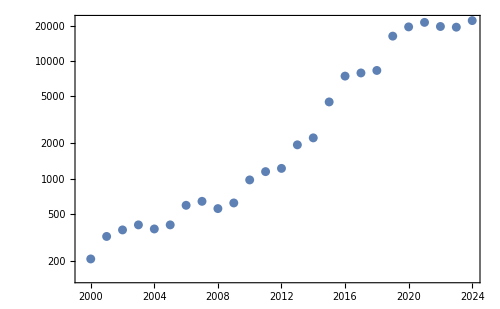

```mathematica
totalSNCountsPerYearPlotSortByMag=ListLogPlot[snCountvsDatesTab2,BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\text{Total SN Counts per Year}",Magnification->1.5],Automatic},{MaTeX["\\text{Year}",Magnification->1.5],None}},Frame->True,ImageSize->500,Frame->True,FrameStyle->Black]
```

```mathematica
totalSNCountsPerYearBrightestPlotSortByMag=ListLogPlot[{snCountsLess15SortByMag,snPeakCountsLess15SortByMag},BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\text{Total SN Counts with }m \\leq 15",Magnification->1.5],Automatic},{MaTeX["\\text{Year}",Magnification->1.5],None}},Frame->True,ImageSize->500,Frame->True,FrameStyle->Black,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{Last Obs. Mag}",Magnification->1.5],0Degree]],Scaled[{.2,.5}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["\\text{Peak Mag}",Magnification->1.5],0Degree]],Scaled[{.2,.85}]]}]
```

-Graphics-

```mathematica
totalSNCountsPerYearBrightestPlot2SortByMag=ListLogPlot[{snCountsLess14SortByMag,snPeakCountsLess14SortByMag},BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\text{Total SN Counts with }m \\leq 14",Magnification->1.5],Automatic},{MaTeX["\\text{Year}",Magnification->1.5],None}},Frame->True,ImageSize->500,Frame->True,FrameStyle->Black,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{Last Obs. Mag}",Magnification->1.5],0Degree]],Scaled[{.2,.3}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["\\text{Peak Mag}",Magnification->1.5],0Degree]],Scaled[{.2,.85}]]}]
```

-Graphics-

```mathematica
Grid[{{totalSNCountsPerYearBrightestPlot2SortByMag},{totalSNCountsPerYearBrightestPlotSortByMag}}]
```

-Graphics-

```mathematica
snHistogramAndCountsAllDatesTotalSortByMag=Grid[{
{snDataOverviewHistogram2,snDataZoomedOverviewHistogram2},{snDataOverviewHistogramPeakMag2,snDataZoomedOverviewHistogramPeakMag2},
{totalSNCountsPerYearPlotSortByMag,totalSNCountsPerYearBrightestPlotSortByMag}}]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"snHistogramAndCountsAllDatesTotal.pdf",snHistogramAndCountsAllDatesTotal]*)
```

```mathematica
snCountsNearOptimiumMag=Table[{datesTab[[i]],Count[magTabSNData2[[i]],mag_/;0<mag<17]},{i,1,Length[datesTab]}]

snPeakCountsNearOptimiumMagm17SortByMag=Table[{datesTab[[i]],Count[peakMagTabSNData2[[i]],mag_/;0<mag<17]},{i,1,Length[datesTab]}];
snPeakCountsNearOptimiumMagm15SortByMag=Table[{datesTab[[i]],Count[peakMagTabSNData2[[i]],mag_/;0<mag<15]},{i,1,Length[datesTab]}];
snPeakCountsNearOptimiumMagm13SortByMag=Table[{datesTab[[i]],Count[peakMagTabSNData2[[i]],mag_/;0<mag<13]},{i,1,Length[datesTab]}];

snCountsNearOptimiumMagPlotSortByMag=ListLogPlot[{snPeakCountsNearOptimiumMagm17SortByMag,snPeakCountsNearOptimiumMagm15SortByMag,snPeakCountsNearOptimiumMagm13SortByMag},BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\text{Observed SN with peak }m < m_{\\rm max}",Magnification->1.5],Automatic},{MaTeX["\\text{Year}",Magnification->1.5],None}},Frame->True,
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],
ImageSize->600,ImagePadding->{{80,20},{70,20}},AspectRatio->1/GoldenRatio,(*PlotRangePadding->None,*)Frame->True,FrameStyle->Black,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["m_{\\rm max} = 17",Magnification->1.65],0Degree]],Scaled[{.85,.875}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["m_{\\rm max} = 15",Magnification->1.65],0Degree]],Scaled[{.85,.7}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.2]]@MaTeX["m_{\\rm max} = 13",Magnification->1.65],0Degree]],Scaled[{.85,.1325}]]}]
```

{{2000,25},{2001,33},{2002,44},{2003,52},{2004,46},{2005,43},{2006,52},{2007,58},{2008,94},{2009,78},{2010,80},{2011,82},{2012,100},{2013,81},{2014,130},{2015,185},{2016,173},{2017,241},{2018,155},{2019,293},{2020,291},{2021,171},{2022,150},{2023,121},{2024,155}}

-Graphics-

```mathematica
(*snCountsOptimumTotal=Grid[{{snCountsNearOptimiumMagPlot,σH0OverH0PlotUpdatedPrecisionMag}}]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"snCountsOptimumTotal.pdf",snCountsOptimumTotal]*)
```

```mathematica
logcumulativesnPeakCountsNearOptimiumMagForFitting2=Transpose[Table[{j,Log10[Count[peakMagTabSNData2[[i]],mag_/;0<mag<j]]},{j,13,19.5,0.1},{i,Length[datesTab]-5,Length[datesTab]}]];
```

```mathematica
logcumulativesnPeakCountsNearOptimiumMag2=Transpose[Table[{j,Log10[Count[peakMagTabSNData2[[i]],mag_/;0<mag<j]]},{j,9,25,0.1},{i,Length[datesTab]-5,Length[datesTab]}]];
```

```mathematica
cumulativeSNPlot2=ListPlot[logcumulativesnPeakCountsNearOptimiumMag2/.{-∞->-10},Joined->True,
BaseStyle->{FontSize->18,FontFamily->"Latin Modern Roman"},
Axes->False,
InterpolationOrder->0,
PlotStyle->{
{AbsoluteThickness[2.5]}},
PlotRange->{{10,22},{-0.1,5}},
FrameLabel->{{MaTeX["\\text{Observed SN with peak }m < m_{\\rm max}",Magnification->1.5],Automatic},{MaTeX["m_{\\rm max}",Magnification->1.5],None}},Frame->True,
FrameTicks->{{logTick[-1,6,1.5,1],logTickNone[-3,3,1.5,1]},{Automatic,Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],
ImageSize->600,ImagePadding->{{80,20},{70,20}},AspectRatio->1/GoldenRatio,(*PlotRangePadding->None,*)Frame->True,FrameStyle->Black,
Epilog->{
(*Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX[
"
\\begin{aligned}
&2019
\\\\
&2020
\\\\
&2021
\\\\
&2022
\\\\
&2023
\\\\
&2024
\\end{aligned}
",Magnification->1.5],0 Degree]],Scaled[{.9,.3}]],*)
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["2019",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["2020",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.2]]@MaTeX["2021",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-2*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[4],.2]]@MaTeX["2022",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-3*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[5],.2]]@MaTeX["2023",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-4*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[6],.2]]@MaTeX["2024",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-5*.085}]],
{Darker[color[1],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215}],Scaled[{.85,.3+.215}]}]},
{Darker[color[2],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-.085}],Scaled[{.85,.3+.215-.085}]}]},
{Darker[color[3],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-2*.085}],Scaled[{.85,.3+.215-2*.085}]}]},
{Darker[color[4],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-3*.085}],Scaled[{.85,.3+.215-3*.085}]}]},
{Darker[color[5],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-4*.085}],Scaled[{.85,.3+.215-4*.085}]}]},
{Darker[color[6],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-5*.085}],Scaled[{.85,.3+.215-5*.085}]}]}}]
```

-Graphics-

```mathematica
logcumulativesnPeakCountsNearOptimiumMagForFittingTab2=Flatten[logcumulativesnPeakCountsNearOptimiumMagForFitting2,1];
```

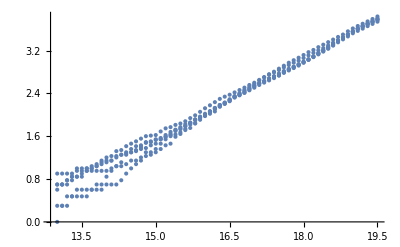

```mathematica
ListPlot[logcumulativesnPeakCountsNearOptimiumMagForFittingTab2]
```

```mathematica
fit1SortByMag=NonlinearModelFit[logcumulativesnPeakCountsNearOptimiumMagForFittingTab2/.{-∞->-10},a*(x+b),{a,b},x]
```

FittedModel[…]

```mathematica
fit2SortByMag=NonlinearModelFit[logcumulativesnPeakCountsNearOptimiumMagForFittingTab2/.{-∞->-10},0.6*(x+b),{b},x]
```

FittedModel[…]

```mathematica
fit1SortByMag["ParameterEstimates"]
fit2SortByMag["ParameterEstimates"]
```

General::munfl: Exp[-845.459] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1215.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1414.56] is too small to represent as a normalized machine number; precision may be lost.

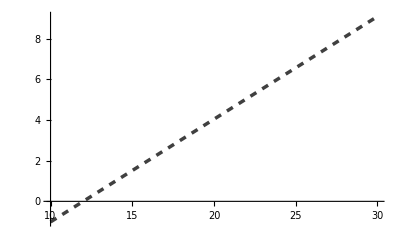

-Graphics-

```mathematica
(*cumulativeSNSlopePlot=Plot[.48(x-11.65),{x,10,30},PlotStyle->{Black,Dashed}]*)
cumulativeSNSlopePlot2=Plot[{.505(x-12.0)(*,.6(x-12.6)*)},{x,10,30},PlotStyle->{Black,Dashed,AbsoluteThickness[2.5],Opacity[.75]}]
totalcumulativeSNPlot2=Show[cumulativeSNPlot2,cumulativeSNSlopePlot2,Epilog->{
(*Inset[Style[Rotate[changeStyle[Darker[color[1],1]]@MaTeX[
"
\\begin{aligned}
&2019
\\\\
&2020
\\\\
&2021
\\\\
&2022
\\\\
&2023
\\\\
&2024
\\end{aligned}
",Magnification->1.5],0 Degree]],Scaled[{.9,.3}]],*)
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["2019",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["2020",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.2]]@MaTeX["2021",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-2*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[4],.2]]@MaTeX["2022",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-3*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[5],.2]]@MaTeX["2023",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-4*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[6],.2]]@MaTeX["2024",Magnification->1.6],0 Degree]],
Scaled[{.9,.3+.215-5*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[6],1]]@MaTeX["\\text{CNF Fit: }F(m) = 10^{0.505(m-12.0)}\\, \\rm{yr^{-1}}",Magnification->1.6],0 Degree]],
Scaled[{.5,.9}]],
{Darker[color[1],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215}],Scaled[{.85,.3+.215}]}]},
{Darker[color[2],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-.085}],Scaled[{.85,.3+.215-.085}]}]},
{Darker[color[3],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-2*.085}],Scaled[{.85,.3+.215-2*.085}]}]},
{Darker[color[4],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-3*.085}],Scaled[{.85,.3+.215-3*.085}]}]},
{Darker[color[5],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-4*.085}],Scaled[{.85,.3+.215-4*.085}]}]},
{Darker[color[6],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775,.3+.215-5*.085}],Scaled[{.85,.3+.215-5*.085}]}]},
{Darker[color[6],1],AbsoluteThickness[3],Arrowheads[0],Dashed,Arrow[{Scaled[{.075,.9}],Scaled[{.18,.9}]}]}}]
```

```mathematica
snPopulationPlotSortByMag=Grid[{{snCountsNearOptimiumMagPlotSortByMag,totalcumulativeSNPlot2}}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/snPopulationPlotSortByMag.pdf",snPopulationPlotSortByMag]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/snPopulationPlotSortByMag.pdf